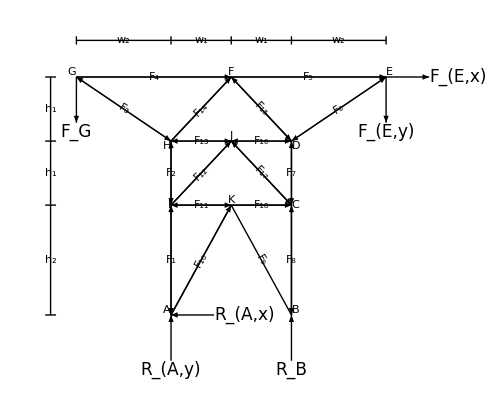

```mathematica
Module[{w1,w2,h1,h2,δ,z1,z2,θ1,θ2,θ3},
w1=7;w2=11;h1=7;h2=12;
δ=5;z1=w1+w2+3;z2=2*h1+h2+4;
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];

Graphics[{Thick,
{EdgeForm@Thick,FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}],

{Arrowheads@0.045,
Arrow[{{-w1-w2,2*h1+h2},{-w1-w2,2*h1+h2-δ}}],
Text[Style[Subscript[Style["F",Italic],"G"],17],{-w1-w2,2*h1+h2-δ},{0,1.2}],

Arrow[{{w1+w2,2*h1+h2},{w1+w2,2*h1+h2-δ}}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2+δ,2*h1+h2}}],
Text[Style[Subscript[Style["F",Italic],Row@{"E,",Style[#1,Italic]}],17],#2,#3]&@@@{{"y",{w1+w2,2*h1+h2-δ},{0,1.2}},{"x",{w1+w2+δ,2*h1+h2},{-1.2,0}}},

Arrow[{{#*w1,-δ},{#*w1,0}}]&/@{-1,1},
Text[Style[Subscript[Style["R",Italic],"B"],17],{w1,-δ},{0,1.2}],

Arrow[{{-w1+δ,0},{-w1,0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#1,Italic]}],17],#2,#3]&@@@{{"x",{-w1+δ,0},{-1.2,0}},{"y",{-w1,-δ},{0,1.2}}}
},

Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15,FrameMargins->Small],#2,#3]&@@@{{"A",{-w1,0},{1.5,-0.5}},{"B",{w1,0},{-1.5,-0.5}},{"C",{w1,h2},{-1.5,0}},{"D",{w1,h1+h2},{-1.5,1}},{"E",{w1+w2,2*h1+h2},{-1,-1}},{"F",{0,2*h1+h2},{0,-1.2}},{"G",{-w1-w2,2*h1+h2},{1,-1}},{"H",{-w1,h1+h2},{1.5,1}},{" I ",{-w1,h2},{1.5,0}},{"J",{0,h1+h2},{0,-1.2}},{"K",{0,h2},{0,-1.2}}},

{Arrowheads@{-0.045,0.045},
Arrow[{{-w1,0},{-w1,h2}}],Arrow[{{-w1,h2},{-w1,h1+h2}}],Arrow[{{-w1,h1+h2},{-w1-w2,2*h1+h2}}],Arrow[{{-w1,h2},{0,h2}}],Arrow[{{-w1,h1+h2},{0,h1+h2}}],Arrow[{{0,h1+h2},{w1,h1+h2}}],Arrow[{{w1,0},{w1,h2}}],Arrow[{{w1,h2},{w1,h1+h2}}],Arrow[{{0,h1+h2},{w1,h2}}],Arrow[{{0,2*h1+h2},{w1,h1+h2}}],Arrow[{{w1,h1+h2},{w1+w2,2*h1+h2}}]},

{Arrowheads@{{0.045,0.315},{-0.045,0.675}},
Arrow[{{-w1,0},{0,h2}}],Arrow[{{-w1,h2},{0,h1+h2}}],Arrow[{{0,h2},{w1,h2}}],Arrow[{{-w1,h1+h2},{0,2*h1+h2}}],Arrow[{{-w1-w2,2*h1+h2},{0,2*h1+h2}}],Arrow[{{0,2*h1+h2},{w1+w2,2*h1+h2}}]},

Text[Rotate[Framed[Style[Subscript[Style["F",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],#3],#2]&@@@{{1,{-w1,h2/2},0},{2,{-w1,h2+h1/2},0},{3,{-w1-w2/2,1.5*h1+h2},-θ2},{4,{-(w1+w2)/2,2*h1+h2},0},{5,{(w1+w2)/2,2*h1+h2},0},{6,{w1+w2/2,1.5*h1+h2},θ2},{7,{w1,h1/2+h2},0},{8,{w1,h2/2},0},{9,{w1/2,h2/2},-θ1},{10,{-w1/2,h2/2},θ1},{11,{-w1/2,h2},0},{12,{-w1/2,h1/2+h2},θ3},{13,{-w1/2,h1+h2},0},{14,{-w1/2,1.5*h1+h2},θ3},{15,{w1/2,1.5*h1+h2},-θ3},{16,{w1/2,h1+h2},0},{17,{w1/2,h1/2+h2},-θ3},{18,{w1/2,h2},0}},

{Thin,
Line[{{-z1,0},{-z1,2*h1+h2}}],Line[{{-0.97*z1,#},{-1.03*z1,#}}]&/@{0,h2,h1+h2,2*h1+h2},
Line[{{-w1-w2,z2},{w1+w2,z2}}],Line[{{#,0.985*z2},{#,1.015*z2}}]&/@{-w1-w2,-w1,0,w1,w1+w2}},

Text[Framed[Style[Subscript[Style["h",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],{-z1,#2}]&@@@{{2,0.5*h2},{1,h2+0.5*h1},{1,h2+1.5*h1}},

Text[Framed[Style[Subscript[Style["w",Italic],#1],17],Background->White,FrameStyle->None,FrameMargins->Tiny],{#2,z2}]&@@@{{2,-w1-0.5*w2},{1,-0.5*w1},{1,0.5*w1},{2,w1+0.5*w2}}
},ImageSize->500]
]
```

```mathematica
2-0.985
```

1.015